```mathematica
(* A Virtual Tour *)

(* Format -> Stylesheet -> Creative -> NaturalColor *)
```

```mathematica
(* This first 'virtual lab' is really a tour, of sorts, to lay out 
  the territory and point out some important features.  Note first,
   that comments are set-off by a combination of parentheses and 
 asterisks.  If you excecute this 'cell', nothing will happen *)
```

```mathematica
I'm typing in a new cell, and I've neglected to use comment marks.  
That's ok...   provided I don't execute the cell.    

If your curiosity gets the best of you, hit "shift enter"  now...
```

Syntax::tsntxi: "I'mtypinginanewcell,andI'veneglectedtousecommentmarks.That'sok...providedIdon'texecutethecell.Ifyourcuriositygetsthebestofyou,hitshift enternow..." is incomplete; more input is needed.

```mathematica
(* What we usually think of as 'variables' are probably better 
described as 'labels'.   And '=' is usually better described
as an assignment operation *)

m = 50                              (* 'assign 50 to the label m'  *)
g = 9.82                          (* 'assign 9.82 to the label g' *)
weight = m*g               (* and so on...                 *)

(* Hit 'shift enter' at any time to run the code in a cell *)
```

50

9.82

491.

```mathematica
(* Did you have to wade through the output to find what you're looking for?   That can be fixed.   A semicolon at the end of a command will
mute the output for that command.  A 'Print[...]' statement can make the final output look real nice - execute this cell and see what I 
mean *)

m = 50;
g = 9.82;
weight = m*g;

Print["The weight of the squirrel was ",weight," Newtons"]
```

The weight of the squirrel was 491. Newtons

```mathematica
(* Now, I really didn't have to re-assign m and g.  Unless I explicitly clear the assigned values or remove the labels, labels and their contents persist from cell to cell.  *)

(* Check out what the next two lines do *)

Print["The weight of the squirrel was ", m g, " Newtons"]
Print["or is it  ...", mg, "...  Newtons? "]
```

The weight of the squirrel was 491. Newtons

or is it  ...mg...  Newtons?

```mathematica
(* Three real important bits here.  1) A space between labels is an implicit multiplication, 2) We can evaluate operations within other statements, and 3) the label 'mg' is distinctly different than m*g *)


(* The carry-over of information from one cell to the next can create a nightmare of impossible-to-untangle dependencies and side-effects.  I strongly recommend that you write the code for any given problem in a SINGLE CELL, and always start that cell with the command 

Remove["Global`*"]   

to remove the variables associated with any code you've run before.  This will be critially important when you start dealing with functions like DSolve[...] *)
```

```mathematica
Remove["Global`*"]         (* Start clean *)

f[t] = t^2 -1;
f[1]
f[2]
```

f[1]

f[2]

```mathematica
(* Notice this probably didn't do what you thought it would... *)

(* The combination f[i] is really an indexed label.  Essentially what you would call Subscript[f, i] if you were working on paper.  (Subscript[f, i] is also an indexed label in Mathematica!)  *)

(* Mathematica will always try to give you the most accurate answer to any question you
 ask it.  Since nothing was assigned to f[1] or f[2], when you asked what f[1] and f[2] were, it told you, to the best of its knowledge *)
```

```mathematica
Remove["Global`*"]

f[t] = t^2 - 1;
f[1] = 4 t + 3;
f[2] = x^3 - 4x + 5;

f[1]
f[2]

(* Execute this.   See what I mean? *)
```

3+4 t

5-4 x+x^3

```mathematica
(* One creates functions by telling Mathematica that a label is 'replace-able'.  Essentially, you add an underscore after the replaceable label *)

Remove["Global`*"]

f[t_] = t^2 - 1;
Print["f[1] = ",f[1]]
Print["f[2] = ",f[2]]

(* Now... t should be replaced by 1 and 2, respectively *)
```

f[1] = 0

f[2] = 3

```mathematica
Remove["Global`*"]

(* There are two kinds of assignments! *)

(* Define a few things *)

x=2;                                 (*  =  Immediate assignment *)
f = x+4;                       (*  =   Immediate assignment *)
g := x^2 -7;              (*  :=  Delayed assignment *)

(* Change the value of x *)

x=10;                 

Print["10 + 4 = ",f]
Print["10^2 -7 = ",g]
```

10 + 4 = 6

10^2 -7 = 93

```mathematica
(* First - I don't necessarily *have* to use functional notation to do a replacement.  Whether I do or not usually depends on the context *)

(* Note the wrong answer in the first line!! *)

(* Immediate assignments tell mathematica to evaluate the right-hand-side of the assignment based on the best information it has at the moment and assign the *result* to the label *)

(* Delayed assignments tell mathematica to store the computation instructions, instead, and update the value of the label accordingly, whenever it's needed *)

(* Since f was immediately assigned, it never saw the update to x *)

(* Some folks will tell you that all functions should be delayed assignments...  I'm not totally convinced that that is true...  *)
```

```mathematica
Remove["Global`*"]

(* Lists are how you form vectors, matrices and tensors... *)

r= {x,y,z};
s= {a,b,c};
m = {{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}};
n = {{n11,n12,n13},{n21,n22,n23},{n31,n32,n33}};

(* Print these in recognizable form *)
Print["r = ",MatrixForm[r]]
Print["m = ",MatrixForm[m]]

Print["m n = ",MatrixForm[m n]]
Print["m*n = ",MatrixForm[m*n]]

Print["These are probably NOT what you want!!!\n"]
Print["Matrix multiplication requires a '.'\n"]

Print["m.n = ",MatrixForm[m.n]]

Print["Checking the output of vector and matrix calculations is a good habit to get into..."]
```

r = (x
y
z)

m = (m11 | m12 | m13
m21 | m22 | m23
m31 | m32 | m33)

m n = (m11 n11 | m12 n12 | m13 n13
m21 n21 | m22 n22 | m23 n23
m31 n31 | m32 n32 | m33 n33)

m*n = (m11 n11 | m12 n12 | m13 n13
m21 n21 | m22 n22 | m23 n23
m31 n31 | m32 n32 | m33 n33)

These are probably NOT what you want!!!

Matrix multiplication requires a '.'

m.n = (m11 n11+m12 n21+m13 n31 | m11 n12+m12 n22+m13 n32 | m11 n13+m12 n23+m13 n33
m21 n11+m22 n21+m23 n31 | m21 n12+m22 n22+m23 n32 | m21 n13+m22 n23+m23 n33
m31 n11+m32 n21+m33 n31 | m31 n12+m32 n22+m33 n32 | m31 n13+m32 n23+m33 n33)

Checking the output of vector and matrix calculations is a good habit to get into...

The time of flight solutions are {{t→(v0 Sin[θ]-√(2 g y0+v0^2 Sin[θ]^2))/g},{t→(v0 Sin[θ]+√(2 g y0+v0^2 Sin[θ]^2))/g}}

The time of flight is (v0 Sin[θ]+√(2 g y0+v0^2 Sin[θ]^2))/g

And the range, R = x0+(v0 Cos[θ] (v0 Sin[θ]+√(2 g y0+v0^2 Sin[θ]^2)))/g

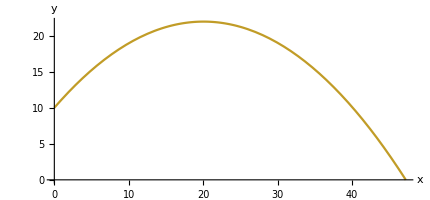

```mathematica
Remove["Global`*"]

(* Let's put these ideas together and have some fun *)

(* Kitten-launch *)

(* Define equations of motion *)
x[t_] = x0 + v0 Cos[θ] t;
y[t_] = y0 + v0 Sin[θ] t - 1/2 g t^2;

r[t_] = {x[t],y[t]};

(* Notice you never have an underscore on the  right-hand side! *)

(*  Find the time-of-flight *)
(* Two equals signs defines equivalence - what you usually mean when you write = on paper *)

Print["The time of flight solutions are ",tof = Solve[{y[t]==0},t]]

(* Run this before proceeding.  The arrows in the output list are 'replacement rules' - we
want the second rule...  this is a little beyond where we are, but easy enough *)

(* Time of Flight *)
Print["The time of flight is ",T = t/.tof[[2]]]     
(* T is t replaced according to the second rule in tof *)

(* Range *)
Print["And the range, R = ",x[T]//Simplify]
(* //Simplify tells mathematica to work a little harder *)

(* Fun - Let's Plot!!  *)

(* We need some numbers *)
x0 = 0;
y0 = 10;
g = 9.82;
v0 = 20;
θ= 50 Degree;     (* Degree is defined to be π/180 in mathematica *)


ParametricPlot[r[t],{t,0,T},AxesLabel->{"x","y"}]
```